## Import application packages

```mathematica
<<ProbabilisticBricks`
```

## Increasing horizontal loads - plastic zone expansion

### Problem initialization

Set the geometry and other parameters using setProblemProperties[nelx, nely, b, h, P, μ], where nelx is the number of bricks per course, nely the number of courses, b and h are the dimensions of the brick, P is the weight of a brick and μ the static friction coefficient

```mathematica
setProblemProperties[50,70,3,1,0.1,0.7];
```

Generate random contacts

```mathematica
generateContacts[];
```

### Compute frames

```mathematica
tmax=12;
frames={};
For[t=0,t≤tmax,t+=0.5,
p=Table[{0,0,0,0,0,0},{nelx}];
p[[5;;8]]={0,0,20,t,0,0};
p=Flatten[p];
setBoundaryConditions[p];
solveProblem[];
AppendTo[frames,{displayWallWithFilter["stress_state"],displayWallWithFilter["contacts_state"]}];
];
```

### Generate & export animation

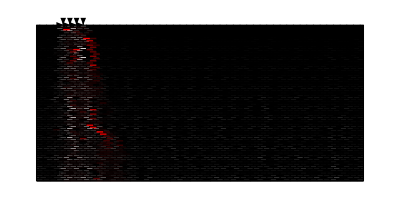
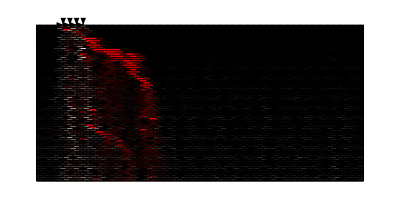
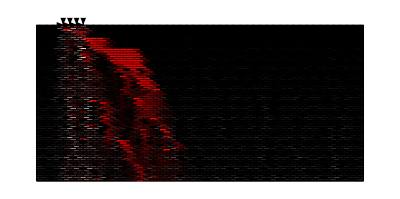
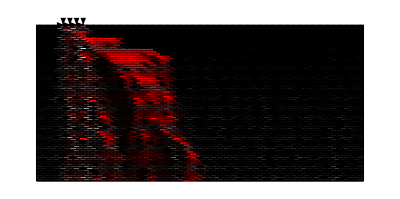
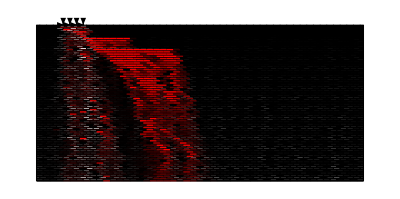
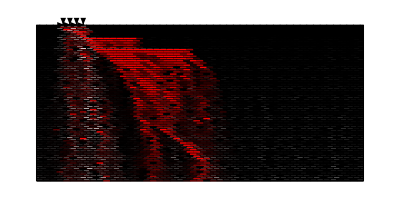
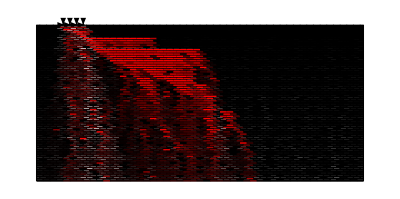
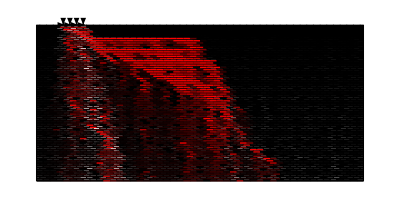

```mathematica
frames[[3;;;;2]]
```

```mathematica
ListAnimate[frames]
```

$Aborted[]

```mathematica
Export["test.gif",frames,ImageSize->1000,"DisplayDurations"->0.3]
```

test.gif

```mathematica
Export["risultati_carichi_h_crescenti_42.pdf",frames[[25,2]],ImageSize->1000,ImageResolution->200]
```

risultati_carichi_h_crescenti_42.pdf

```mathematica
{5,11,19,25}
```